```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Viktor\Desktop\Projekt MatStat\KTH-Mathematica\Statistics

```mathematica
Once[Get["Project2.m","IX1501"]]
```

```mathematica
?randomExample
```

```mathematica
ClearAll["`*"]
```

```mathematica
n=10000;
𝕩=randomNumber[1, n];
Short[𝕩];
𝕩sort=Sort[𝕩];
```

```mathematica
Δ=1/n;
```

```mathematica
𝕡data=Δ/2+Range[0,1-Δ,Δ]//N;
```

```mathematica
Short[𝕡data];
```

```mathematica
𝕩𝕡data=Transpose[{𝕩sort,𝕡data}];
```

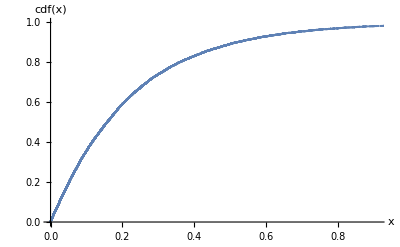

```mathematica
ListPlot[𝕩𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]}]
```

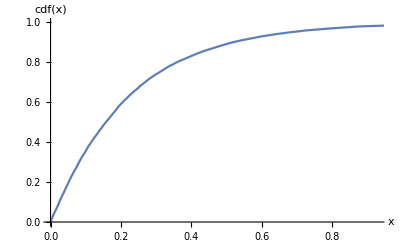

```mathematica
qdata=Table[{Quantile[𝕩,q],q},{q,0,1,0.01}];
ListLinePlot[qdata,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]}]
```

```mathematica
x=Mean[𝕩]
```

0.225264

```mathematica
s=StandardDeviation[𝕩]
```

0.227002

```mathematica
𝒩=NormalDistribution[x,s]
```

NormalDistribution[0.225264,0.227002]

```mathematica
𝕡model=CDF[𝒩,𝕩sort];
```

```mathematica
comparedata=Transpose[{𝕡model,𝕡data}];
```

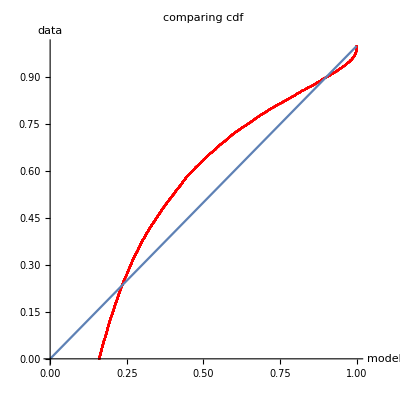

```mathematica
dataplot=ListPlot[comparedata,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing cdf",AspectRatio->Automatic];
lineplot=Plot[x,{x,0,1}];
Show[dataplot,lineplot]
```

```mathematica
Clear[α,β];
```

```mathematica
𝒢=EstimatedDistribution[𝕩,NormalDistribution[α,β]]
```

NormalDistribution[0.225264,0.226991]

```mathematica
𝕡model=CDF[𝒢,𝕩sort];
𝕩sort;
```

```mathematica
comparedata=Transpose[{𝕡model,𝕡data}];
```

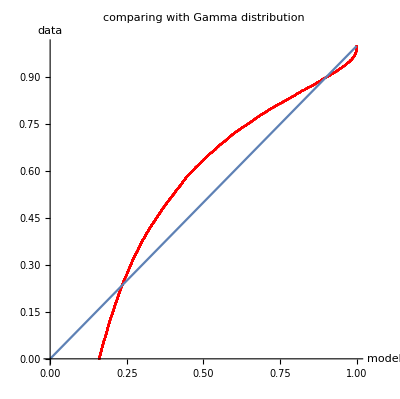

```mathematica
dataplot=ListPlot[comparedata,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing with Gamma distribution",AspectRatio->Automatic];
lineplot=Plot[x,{x,0,1}];
Show[dataplot,lineplot]
```